```mathematica
𝒞[expr_[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_][M1_,M2_,M3_,M4_]]:=ReplaceAll[expr[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][M1,M2,M3,M4],{ω1->ω2/(1+ω2-ω1),ω2->ω1/(1+ω2-ω1),ϕ1->ϕ3,ϕ3->ϕ1,ϕ2->ϕ4,ϕ4->ϕ2,M1->M3,M3->M1,M2->M4,M4->M2}]
𝒫[expr_[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_][M1_,M2_,M3_,M4_]]:=ReplaceAll[expr[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][M1,M2,M3,M4],{ω1->(1+ω2-ω1)/ω2,ω2->1/ω2,ϕ1->ϕ2,ϕ2->ϕ1,ϕ3->ϕ4,ϕ4->ϕ3,M1->M2,M2->M1,M3->M4,M4->M3}]
ℛ[expr_[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_][M1_,M2_,M3_,M4_]]:=ReplaceAll[expr[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][M1,M2,M3,M4],{ω1->ω1/ω2,ω2->1/ω2,ϕ3->ϕ4,ϕ4->ϕ3,M3->M4,M4->M3}]
𝒮[expr_[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_][M1_,M2_,M3_,M4_]]:=ReplaceAll[expr[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][M1,M2,M3,M4],{ω1->1/ω1,ω2->(1+ω2-ω1)/ω1,ϕ1->ϕ4,ϕ4->ϕ1,ϕ2->ϕ3,ϕ3->ϕ2,M1->M4,M4->M1,M2->M3,M3->M2}]
```

```mathematica
EXPR[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_][Ma_,Mb_,Mc_,Md_]=Simplify[(#+𝒫@#+𝒞@#+ℛ@#+𝒫@𝒞@#+ℛ@𝒞@#+ℛ@𝒫@#+ℛ@𝒫@𝒞@#)&@ℳ0[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][Ma,Mb,Mc,Md]+(#+ℛ@#)&@ℳ1[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][Ma,Mb,Mc,Md]];
```

```mathematica
EXPR[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][M1,M2,M3,M4]
```

ℳ0[1/ω1,(1-ω1+ω2)/ω1][ϕ4,ϕ3,ϕ2,ϕ1][M4,M3,M2,M1]+ℳ0[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][M1,M2,M3,M4]+ℳ0[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][M1,M2,M4,M3]+ℳ0[ω2/ω1,(1-ω1+ω2)/ω1][ϕ3,ϕ4,ϕ2,ϕ1][M3,M4,M2,M1]+ℳ0[1/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ4,ϕ3,ϕ1,ϕ2][M4,M3,M1,M2]+ℳ0[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][M3,M4,M1,M2]+ℳ0[1-ω1+ω2,ω2][ϕ2,ϕ1,ϕ3,ϕ4][M2,M1,M3,M4]+ℳ0[(1-ω1+ω2)/ω2,1/ω2][ϕ2,ϕ1,ϕ4,ϕ3][M2,M1,M4,M3]+ℳ1[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][M1,M2,M3,M4]+ℳ1[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][M1,M2,M4,M3]

```mathematica
Simplify@EXPR[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][M1,M2,M3,M4]
```

ℳ0[1/ω1,(1-ω1+ω2)/ω1][ϕ4,ϕ3,ϕ2,ϕ1][M4,M3,M2,M1]+ℳ0[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][M1,M2,M3,M4]+ℳ0[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][M1,M2,M4,M3]+ℳ0[ω2/ω1,(1-ω1+ω2)/ω1][ϕ3,ϕ4,ϕ2,ϕ1][M3,M4,M2,M1]+ℳ0[1/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ4,ϕ3,ϕ1,ϕ2][M4,M3,M1,M2]+ℳ0[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][M3,M4,M1,M2]+ℳ0[1-ω1+ω2,ω2][ϕ2,ϕ1,ϕ3,ϕ4][M2,M1,M3,M4]+ℳ0[(1-ω1+ω2)/ω2,1/ω2][ϕ2,ϕ1,ϕ4,ϕ3][M2,M1,M4,M3]+ℳ1[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][M1,M2,M3,M4]+ℳ1[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][M1,M2,M4,M3]

```mathematica
ℐ1[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_][M1_,M2_,M3_,M4_]:=If[1>ω1,-4 g^2(NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,0,1},{y,0,(ω1-ω2+x ω2)/ω1-λ}]+NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,0,1},{y,(ω1-ω2+x ω2)/ω1+λ,1}]-2/λ NIntegrate[ω2/ω1 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[(ω1-ω2+x ω2)/ω1]ϕ3[((ω1-ω2+x ω2)/ω1 )ω1]ϕ4[x],{x,0,1}]),0];
ℐ2[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_][M1_,M2_,M3_,M4_]:=If[ω2>ω1,-4 g^2(NIntegrate[ω1/(y ω1-x)^2 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[y]ϕ3[x]ϕ4[((y-1) ω1+ω2)/ω2],{x,0,1},{y,0,x/ω1-λ}]+NIntegrate[ω1/(y ω1-x)^2 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[y]ϕ3[x]ϕ4[((y-1) ω1+ω2)/ω2],{x,0,1},{y,x/ω1+λ,1}]-2/λ NIntegrate[1/ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[x/ω1]ϕ3[x]ϕ4[((x/ω1-1) ω1+ω2)/ω2],{x,0,1}]),0];
ℐ3[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_][Ma_,Mb_,Mc_,Md_]:=If[(ω2>ω1)&&(ω1>1),-(4 π)/Nc NIntegrate[(Mc^2+Md^2/ω2+Ma^2/(x-ω1)+Ma^2/(x-1)-Ma^2/(x-ω1+ω2)-Ma^2/x)ϕ1[(x-ω1+ω2)/(1+ω2-ω1)]ϕ2[x/ω1]ϕ3[x]ϕ4[(x-ω1+ω2)/ω2],{x,0,1}],0];
```

```mathematica
ℳ1[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_][Ma_,Mb_,Mc_,Md_]=((#+𝒮[#])&[(*If[1>ω1,-4 g^2 NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,0,1},{y,0,1}],0]*)
ℐ1[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][Ma,Mb,Mc,Md]])+((#+𝒞[#])&[(*If[ω2>ω1,-4 g^2 NIntegrate[ω1/(y ω1-x)^2 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[y]ϕ3[x]ϕ4[((y-1) ω1+ω2)/ω2],{x,0,1},{y,0,1}],0]*)
ℐ2[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][Ma,Mb,Mc,Md]])+((#+𝒮[#]+𝒫[#]+𝒞[#])&[ℐ3[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][Ma,Mb,Mc,Md]])
```

ℐ1[1/ω1,(1-ω1+ω2)/ω1][ϕ4,ϕ3,ϕ2,ϕ1][Md,Mc,Mb,Ma]+ℐ1[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][Ma,Mb,Mc,Md]+ℐ2[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][Ma,Mb,Mc,Md]+ℐ2[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][Mc,Md,Ma,Mb]+ℐ3[1/ω1,(1-ω1+ω2)/ω1][ϕ4,ϕ3,ϕ2,ϕ1][Md,Mc,Mb,Ma]+ℐ3[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][Ma,Mb,Mc,Md]+ℐ3[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][Mc,Md,Ma,Mb]+ℐ3[(1-ω1+ω2)/ω2,1/ω2][ϕ2,ϕ1,ϕ4,ϕ3][Mb,Ma,Md,Mc]

```mathematica
ℳ1[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][M1,M2,M3,M4]
```

ℐ1[1/ω1,(1-ω1+ω2)/ω1][ϕ4,ϕ3,ϕ2,ϕ1][M4,M3,M2,M1]+ℐ1[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][M1,M2,M3,M4]+ℐ2[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][M1,M2,M3,M4]+ℐ2[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][M3,M4,M1,M2]+ℐ3[1/ω1,(1-ω1+ω2)/ω1][ϕ4,ϕ3,ϕ2,ϕ1][M4,M3,M2,M1]+ℐ3[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][M1,M2,M3,M4]+ℐ3[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][M3,M4,M1,M2]+ℐ3[(1-ω1+ω2)/ω2,1/ω2][ϕ2,ϕ1,ϕ4,ϕ3][M2,M1,M4,M3]

```mathematica
ℐ1[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][M1,M2,M3,M4]
```

If[1>ω1,-4 g^2 (NIntegrate[((ω1 ω2) ϕ1[(x ω2)/(1+ω2-ω1)] ϕ2[y] ϕ3[y ω1] ϕ4[x])/((y-1) ω1+(1-x) ω2)^2,{x,0,1},{y,0,(ω1-ω2+x ω2)/ω1-λ}]+NIntegrate[((ω1 ω2) ϕ1[(x ω2)/(1+ω2-ω1)] ϕ2[y] ϕ3[y ω1] ϕ4[x])/((y-1) ω1+(1-x) ω2)^2,{x,0,1},{y,(ω1-ω2+x ω2)/ω1+λ,1}]-(2 NIntegrate[(ω2 ϕ1[(x ω2)/(1+ω2-ω1)] ϕ2[(ω1-ω2+x ω2)/ω1] ϕ3[((ω1-ω2+x ω2) ω1)/ω1] ϕ4[x])/ω1,{x,0,1}])/λ),0]

```mathematica
ℐ1[1/ω1,(1-ω1+ω2)/ω1][ϕ4,ϕ3,ϕ2,ϕ1][M4,M3,M2,M1]
```

If[1>1/ω1,-4 g^2 (NIntegrate[((1-ω1+ω2) ϕ4[(x (1-ω1+ω2))/(ω1 (1+(1-ω1+ω2)/ω1-1/ω1))] ϕ3[y] ϕ2[y/ω1] ϕ1[x])/(ω1 ω1 ((y-1)/ω1+((1-x) (1-ω1+ω2))/ω1)^2),{x,0,1},{y,0,(1/ω1-(1-ω1+ω2)/ω1+(x (1-ω1+ω2))/ω1)/(1/ω1)-λ}]+NIntegrate[((1-ω1+ω2) ϕ4[(x (1-ω1+ω2))/(ω1 (1+(1-ω1+ω2)/ω1-1/ω1))] ϕ3[y] ϕ2[y/ω1] ϕ1[x])/(ω1 ω1 ((y-1)/ω1+((1-x) (1-ω1+ω2))/ω1)^2),{x,0,1},{y,(1/ω1-(1-ω1+ω2)/ω1+(x (1-ω1+ω2))/ω1)/(1/ω1)+λ,1}]-(2 NIntegrate[((1-ω1+ω2) ϕ4[(x (1-ω1+ω2))/(ω1 (1+(1-ω1+ω2)/ω1-1/ω1))] ϕ3[(1/ω1-(1-ω1+ω2)/ω1+(x (1-ω1+ω2))/ω1)/(1/ω1)] ϕ2[(1/ω1-(1-ω1+ω2)/ω1+(x (1-ω1+ω2))/ω1)/(ω1/ω1)] ϕ1[x])/(ω1/ω1),{x,0,1}])/λ),0]

```mathematica
Simplify@(((1-ω1+ω2) ϕ4[(x (1-ω1+ω2))/(ω1 (1+(1-ω1+ω2)/ω1-1/ω1))] ϕ3[y] ϕ2[y/ω1] ϕ1[x])/(ω1 ω1 ((y-1)/ω1+((1-x) (1-ω1+ω2))/ω1)^2))
```

-((-1+ω1-ω2) ϕ1[x] ϕ2[y/ω1] ϕ3[y] ϕ4[(x (1-ω1+ω2))/ω2])/(y-ω1+x (-1+ω1-ω2)+ω2)^2

```mathematica
If[ω2>ω1,-4 g^2 Hold@(NIntegrate[ω1/(y ω1-x)^2 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[y]ϕ3[x]ϕ4[((y-1) ω1+ω2)/ω2],{x,0,1},{y,0,x/ω1-λ}]+NIntegrate[ω1/(y ω1-x)^2 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[y]ϕ3[x]ϕ4[((y-1) ω1+ω2)/ω2],{x,0,1},{y,x/ω1+λ,1}]-2/λ NIntegrate[1/ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[x/ω1]ϕ3[x]ϕ4[((x/ω1-1) ω1+ω2)/ω2],{x,0,1}]),0]/.{ω1->ω2/(1-ω1+ω2),ω2->ω1/(1-ω1+ω2),ϕ1->ϕ3,ϕ3->ϕ1,ϕ2->ϕ4,ϕ4->ϕ2}
```

If[ω1/(1-ω1+ω2)>ω2/(1-ω1+ω2),-4 g^2 Hold[NIntegrate[(ω2 ϕ3[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ4[y] ϕ1[x] ϕ2[(((y-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/((1-ω1+ω2) ((y ω2)/(1-ω1+ω2)-x)^2),{x,0,1},{y,0,x/(ω2/(1-ω1+ω2))-λ}]+NIntegrate[(ω2 ϕ3[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ4[y] ϕ1[x] ϕ2[(((y-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/((1-ω1+ω2) ((y ω2)/(1-ω1+ω2)-x)^2),{x,0,1},{y,x/(ω2/(1-ω1+ω2))+λ,1}]-(2 NIntegrate[(ϕ3[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ4[x/(ω2/(1-ω1+ω2))] ϕ1[x] ϕ2[(((x/(ω2/(1-ω1+ω2))-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/(ω2/(1-ω1+ω2)),{x,0,1}])/λ],0]

```mathematica
Simplify@%
```

If[ω1^2+ω2+ω2^2<ω1+2 ω1 ω2,-4 g^2 Hold[NIntegrate[(ω2 ϕ3[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ4[y] ϕ1[x] ϕ2[(((y-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/((1-ω1+ω2) ((y ω2)/(1-ω1+ω2)-x)^2),{x,0,1},{y,0,x/(ω2/(1-ω1+ω2))-λ}]+NIntegrate[(ω2 ϕ3[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ4[y] ϕ1[x] ϕ2[(((y-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/((1-ω1+ω2) ((y ω2)/(1-ω1+ω2)-x)^2),{x,0,1},{y,x/(ω2/(1-ω1+ω2))+λ,1}]-(2 NIntegrate[(ϕ3[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ4[x/(ω2/(1-ω1+ω2))] ϕ1[x] ϕ2[(((x/(ω2/(1-ω1+ω2))-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/(ω2/(1-ω1+ω2)),{x,0,1}])/λ],0]

```mathematica
ReleaseHold@%
```

If[ω1^2+ω2+ω2^2<ω1+2 ω1 ω2,-4 g^2 (NIntegrate[(ω2 ϕ3[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ4[y] ϕ1[x] ϕ2[(((y-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/((1-ω1+ω2) ((y ω2)/(1-ω1+ω2)-x)^2),{x,0,1},{y,0,x/(ω2/(1-ω1+ω2))-λ}]+NIntegrate[(ω2 ϕ3[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ4[y] ϕ1[x] ϕ2[(((y-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/((1-ω1+ω2) ((y ω2)/(1-ω1+ω2)-x)^2),{x,0,1},{y,x/(ω2/(1-ω1+ω2))+λ,1}]-(2 NIntegrate[(ϕ3[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ4[x/(ω2/(1-ω1+ω2))] ϕ1[x] ϕ2[(((x/(ω2/(1-ω1+ω2))-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/(ω2/(1-ω1+ω2)),{x,0,1}])/λ),0]

```mathematica
If[ω1^2+ω2+ω2^2<ω1+2 ω1 ω2,-4 g^2 (NIntegrate[(ω2 ϕ1[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ2[y] ϕ3[x] ϕ4[(((y-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/((1-ω1+ω2) ((y ω2)/(1-ω1+ω2)-x)^2),{x,0,1},{y,0,x/(ω2/(1-ω1+ω2))-λ}]+NIntegrate[(ω2 ϕ1[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ2[y] ϕ3[x] ϕ4[(((y-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/((1-ω1+ω2) ((y ω2)/(1-ω1+ω2)-x)^2),{x,0,1},{y,x/(ω2/(1-ω1+ω2))+λ,1}]-(2 NIntegrate[(ϕ1[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ2[x/(ω2/(1-ω1+ω2))] ϕ3[x] ϕ4[(((x/(ω2/(1-ω1+ω2))-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/(ω2/(1-ω1+ω2)),{x,0,1}])/λ),0]
```

If[ω1^2+ω2+ω2^2<ω1+2 ω1 ω2,-4 g^2 Simplify[NIntegrate[(ω2 ϕ1[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ2[y] ϕ3[x] ϕ4[(((y-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/((1-ω1+ω2) ((y ω2)/(1-ω1+ω2)-x)^2),{x,0,1},{y,0,x/(ω2/(1-ω1+ω2))-λ}]+NIntegrate[(ω2 ϕ1[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ2[y] ϕ3[x] ϕ4[(((y-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/((1-ω1+ω2) ((y ω2)/(1-ω1+ω2)-x)^2),{x,0,1},{y,x/(ω2/(1-ω1+ω2))+λ,1}]-(2 NIntegrate[(ϕ1[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ2[x/(ω2/(1-ω1+ω2))] ϕ3[x] ϕ4[(((x/(ω2/(1-ω1+ω2))-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/(ω2/(1-ω1+ω2)),{x,0,1}])/λ],0]

```mathematica
(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))//Simplify
```

ω1-ω2+x (1-ω1+ω2)

```mathematica
x/(ω2/(1-ω1+ω2))//Simplify
```

(x (1-ω1+ω2))/ω2

```mathematica
(((x/(ω2/(1-ω1+ω2))-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))//Simplify
```

(x+ω1-x ω1-ω2+x ω2)/ω1

```mathematica
(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))//Simplify
```

ω1-ω2+x (1-ω1+ω2)

```mathematica
(((y-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))//Simplify
```

1+((-1+y) ω2)/ω1

```mathematica
ω2/((1-ω1+ω2) ((y ω2)/(1-ω1+ω2)-x)^2)//Simplify
```

```mathematica
((1-ω1+ω2)/ω2)/(x (-1+ω1-ω2)/ω2+y )^2
```

(1-ω1+ω2)/((y+(x (-1+ω1-ω2))/ω2)^2 ω2)

```mathematica
Assuming[0<x<1&&0<y<1,Refine@ω1-ω2+x (1-ω1+ω2)]
```

ω1-ω2+x (1-ω1+ω2)

```mathematica
ω2p[ω1_][M1_,M2_,M3_,M4_]:=1/(2 (M3^2 ω1-M2^2))(-√((M1^2 (-ω1)+M2^2 ω1-M2^2-M3^2 ω1^2+M3^2 ω1+M4^2 ω1)^2-4 (M4^2 ω1-M4^2 ω1^2) (M3^2 ω1-M2^2))+M1^2 ω1-M2^2 ω1+M2^2+M3^2 ω1^2-M3^2 ω1-M4^2 ω1)(*transform ω1 to ω2, your definition, solution 1*)
```

```mathematica
Sω1[ω1_][M1_,M2_,M3_,M4_]:=(M1^2/(1-ω1+ω2p[ω1][M1,M2,M3,M4])+M2^2/ω1)(1+ω2p[ω1][M1,M2,M3,M4]);
```

```mathematica
ω1S[s_][M1_,M2_,M3_,M4_]:=(-M1^2+M2^2+s-√s √((M1^4+(M2^2-s)^2-2 M1^2 (M2^2+s))/s))/(M3^2-M4^2+s+√s √((M3^4+(M4^2-s)^2-2 M3^2 (M4^2+s))/s));
ω2S[s_][M1_,M2_,M3_,M4_]:=(-M3^2+M4^2+s-√s √((M3^4+(M4^2-s)^2-2 M3^2 (M4^2+s))/s))/(M3^2-M4^2+s+√s √((M3^4+(M4^2-s)^2-2 M3^2 (M4^2+s))/s));
```

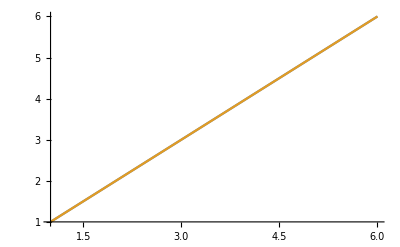

```mathematica
Plot[{Sω1[ω1S[s][1,2,3,4]][1,2,3,4],s},{s,1,6}]
```